0

1.5

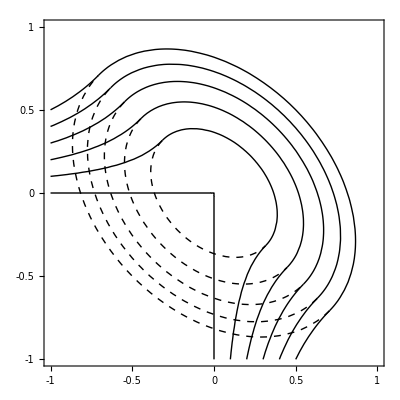

/Volumes/DATA/Documents/Manuscripts/Thesis/ch-fracture/asymmetric_energy/a_15.pdf

```mathematica
ClearAll[a,b,c]
d=0;
g[b_,c_]:=1/2(b+c)^2 + (b^2+2*d^2+c^2) - a *(b+c)^2;

a=0
c1=ContourPlot[g[b,c],{b,-1,1},{c,-1,1},Contours->{0,0.2,0.4,0.6,0.8,1.0},RegionFunction->Function[{b,c},b+c>0],ContourShading->None,FrameTicks->{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1},None,None},LabelStyle->Larger];

c2=ContourPlot[g[b,c],{b,-1,1},{c,-1,1},Contours->{0,0.2,0.4,0.6,0.8,1.0},RegionFunction->Function[{b,c},b+c<0],ContourShading->None,ContourStyle->Dashed,FrameTicks->{{-1,0,1},{-1,0,1}}];


a=1.5
c3=ContourPlot[g[b,c],{b,-1,1},{c,-1,1},Contours->{0,0.2,0.4,0.6,0.8,1.0},RegionFunction->Function[{b,c},b+c<0],ContourShading->None,FrameTicks->{{-1,0,1},{-1,0,1}}];

s=Show[c1,c2,c3]
Export["/Volumes/DATA/Documents/Manuscripts/Thesis/ch-fracture/asymmetric_energy/a_15.pdf",s]
```